# R51 Triplet + C2H2 1st

## MESMER

## Functions

### Documentation

ReadMESMERGrainDoS[FileName] := Read grained DoS from *.test for further plotting. Output: {  {IM1,TS1,IM2,P1,...},  {  DoS-of-IM1, DoS-of-TS1, DoS-of-IM2, DoS-of-P1,...  }} 
ReadMESMERGrainedSpeciesProfile [FileName]: Read Grained species profile from MESMER *.test

ReadMESMERpT[FileName]: Read p and T;
ReadMESMERGrainTopHillTest[FileName]: TopEnergyHill and Egrain test
ReadMESMEREquilFraction [FileName]: Read Equilibrium Faction for isomers from MESMER *.test
ReadMESMEREgienvalue [FileName]: Read Eigenvalues from MESMER *.test

ReadMESMERAverageEnergy [FileName]:  Read <E> from MESMER *.test
ReadMESMERSpeicesProfile[FileName]: Read species profile from MESMER *.test. Output Species profile matrix

MESMERGrainedSpeciesProfileManipulate[GrainedProfileData, species] :  make animation of Grained Species profile. Input: GrainedProfileData: output of ReadMESMERGrainedSpeciesProfile,  species: name of isomer, such as "P1","IM1"
MESMERAverageEnergyPlot[AverEData]: output of ReadMESMERAverageEnergy as input
MESMERSpeciesProfilePlot[ProfileData] : plot species profile as a function of time . Input: output of ReadMESMERSpeicesProfile
MESMERFitRate [SpeciesProfileData,FitType]: fitting species profile for reaction rate constants. Input: SpeciesProfileData should be Data⟦1,2 ;;, {1, x}⟧ where Data is the output of ReadMESMERSpeicesProfile

FitType = 1:
A<=> B forward  k_f  backward k_b Initial A_0=1. A<->B forwardk_f backwardk_b. FitProfile should be the reactant profile
A = k_b/(k_f+k_b)+(1-k_b/(k_f+k_b))ⅇ^(-(k_f+k_b)t)
t<< kf+kb => B= A0*kf*t, therefore plot R71C2H3(t)/t
ln(-dA/dt)=ln(kf)-(kf+kb)*t, therefore we can obtain kf and kb from a ln(-dA/dt)-t plot by taking the slop and intercept

FitType = 2:
A<=> B forward  k_f  backward k_b Initial A_0=1. A<->B forwardk_f backwardk_b. FitProfile should be the product profile
B= k_f/(k_f+k_b)(1-ⅇ^(-(k_f+k_b)t))

FitType = 3:
A => Sink. forward k_f. Initial A_0 = 1.  FitProfile should be the reactant profile
A = A_0 ⅇ^-k_ft

ReadMESMERMicroRate [UNFINISHED!!!]
ReadMESMERCTSTRate [UNFINISHED!!!]
MESMERMicroRatePlot  [UNFINISHED!!!]
MESMERMicroRateTimesBoltzmann  [UNFINISHED!!!]
MESMERMicroRateTimesGrainedSpeciesProfile  [UNFINISHED!!!]
MESMERGrainedSpeceisProfileOverBoltzmann  [UNFINISHED!!!]

### Functions

```mathematica
ReadMESMERpT[Name_]:=Module[  (*Read pressure and temperature from *.test*)
{str,iRead,str1,conc,temp,pres},
str=OpenRead[Name];
iRead=True;
While[iRead,
str1=Read[str,String];
If[str1==EndOfFile,Print["Neither 'conc' nor 'temp' is found"];iRead=False];
If[StringCases[str1,RegularExpression["Condition"]]≠ {},
iRead=False;
conc=Read[StringToStream[StringReplace[StringCases[str1,RegularExpression["conc = (.+?),"]],{"conc = "-> "",","-> ""}]⟦1⟧],Number];
temp=Read[StringToStream[StringReplace[StringCases[str1,RegularExpression["temp = (.+?),"]],{"temp = "-> "",","-> ""}]⟦1⟧],Number];
pres=conc/(6.02*10^23)*temp*82.0574587
];
]
Close[str];Clear[str];
{conc,pres,temp}
];
ReadMESMERGrainTopHillTest[Name_]:=Module[  (*Read qtot,sumc,sumg in *.test, and test whether grain-size/TopEnergyHill are suitable*)
{str,iRead,str1,species,Data,DataName,txt,buffer},
str=OpenRead[Name];
iRead=True;
DataName={{"Species Name","Temperature","(Qanaly-Qcell)/Qanaly","(Qgrain-Qcell)/Qcell"}};
txt="Test rovibronic density of states for: ";
While[iRead,
str1=Read[str,String];
If[str1==EndOfFile,(*Print["No Test rovibronic density of states is found"];*)iRead=False;Break[]];
Data={0,0,0,0};
If[StringCases[str1,RegularExpression[txt]]≠ {},
(*iRead=False;*)
species=StringReplace[str1,{txt-> ""}];
str1=Read[str,String];
str1=Read[str,String];
str1=Read[str,String];
While[str1≠ "}",
buffer=ReadList[StringToStream[str1],Number];
AppendTo[Data,buffer];
str1=Read[str,String](*;str1//Print;*)
];
AppendTo[DataName,{species,Data⟦-2,1⟧,(Data⟦-2,3⟧-Data⟦-2,2⟧)/Data⟦-2,2⟧,(Data⟦-2,4⟧-Data⟦-2,3⟧)/Data⟦-2,3⟧}];
];
];
Close[str];Clear[str];DataName//MatrixForm
];
ReadMESMERGrainDoS[Name_]:=Module[  (*Read grained DoS from *.test for further plotting*)
{str,iRead,txt,str1,species,buffer,Data,DataAll},
str=OpenRead[Name];
iRead=True;
txt="Grain rovibronic density of states of ";
species={};
DataAll={};
While[iRead,
str1=Read[str,String];
If[str1==EndOfFile,iRead=False;Break[]];
Data={};
If[StringCases[str1,RegularExpression[txt]]≠ {},
(*iRead=False;*)
AppendTo[species,StringReplace[str1,{txt-> ""}]];
str1=Read[str,String];
str1=Read[str,String];
While[str1≠ "}",
buffer=ReadList[StringToStream[str1],Number];
AppendTo[Data,buffer];
str1=Read[str,String]
];
AppendTo[DataAll,Data];
];
];
Close[str];Clear[str];{species,DataAll}
];
ReadMESMERMicroRate[Name_]:=Module[  (*Read MESMER *.test output file*)
{str},
str=OpenRead[Name];

Close[str];Clear[str];
];
ReadMESMERSpeicesProfile[Name_]:=Module[  (*Read species profile from MESMER *.test*)
{str,txt,str1,Data,iRead,buffer},
str=OpenRead[Name];
txt="Print time dependent species and product profiles";
iRead=True;
Data={};
While[iRead,
str1=Read[str,String];
If[str1== EndOfFile,iRead=False;Break[]];
If[StringCases[str1,txt]≠ {},
iRead=False;
str1=Read[str,String];
str1=Read[str,String];
buffer=ReadList[StringToStream[str1],Word];
AppendTo[Data,buffer];
str1=Read[str,String];
While[str1≠ "}",
buffer=ReadList[StringToStream[str1],Number];
AppendTo[Data,buffer];
str1=Read[str,String]
];
];
];
Close[str];Clear[str];Data//MatrixForm
];
ReadMESMEREquilFraction[Name_]:=Module[  (*Read Equilibrium Faction for isomers from MESMER*.test*)
{str,txt,iRead,Data,str1,buffer1,buffer,buffer2},
str=OpenRead[Name];
txt="Equilibrium Fraction for";
iRead=True;
Data={};
While[iRead,
str1=Read[str,String];
If[str1== EndOfFile,iRead=False;Break[]];
If [StringCases[str1,RegularExpression[txt]]≠ {},
buffer1=StringReplace[str1,{txt-> "","="-> " "}];
buffer=ReadList[StringToStream[buffer1],{Word,Number}];
AppendTo[Data,buffer⟦1⟧]
];
];
Close[str];Clear[str];Data
];
ReadMESMEREgienvalue[Name_]:=Module[  (*Read Eigenvalues from MESMER *.test*)
{str,txt,iRead,Data,str1,buffer},
str=OpenRead[Name];
txt="Total number of eigenvalues";
iRead=True;
Data={};
While[iRead==True,
str1=Read[str,String];
If[str1==EndOfFile,iRead=False;Break[]];
If[StringCases[str1,txt]≠ {},
iRead=False;
str1=Read[str,String];
str1=Read[str,String];
str1=Read[str,String];
While[str1≠ "}",
buffer=ReadList[StringToStream[str1],Number]⟦1⟧;
AppendTo[Data,buffer];
str1=Read[str,String];
];
];
];
Close[str];Clear[str];Data
];
ReadMESMERAverageEnergy[Name_]:=Module[  (*Read <E> from MESMER *.test*)
{str,txt,str1,species,Data,DataAll,buffer,iRead},
str=OpenRead[Name];
(*txt="average energy in each isomer (kJ/mol)";*)
txt="average energy in each isomer";
iRead=True;
species={};
DataAll={};
While[iRead,
str1=Read[str,String];
If[str1==EndOfFile,iRead=False;Print["NO average energy in each isomoer is found"];Abort[]];
If[StringCases[str1,RegularExpression[txt]]≠ {},iRead=False];
];
str1=Read[str,String];
While[str1≠ "}",
AppendTo[species,StringReplace[str1,": "-> ""]];
Data={};
str1=Read[str,String];
str1=Read[str,String];
While[StringCases[str1,RegularExpression["^ "]]≠{} ,
buffer=ReadList[StringToStream[str1],Number];
AppendTo[Data,buffer];
str1=Read[str,String];
];
AppendTo[DataAll,Data];
];
Close[str];Clear[str];{species,DataAll}
];
ReadMESMERGrainedSpeciesProfile[Name_]:=Module[  (*Read Grained species profile from MESMER *.test*)
{str,txt,str1,species,span,Data,DataAll,buffer,iRead,time,temp1,i},
str=OpenRead[Name];
txt="Grained species profile:";
iRead=True;
species={};
Data={};
span={};
While[iRead,
str1=Read[str,String];
If[str1==EndOfFile,iRead=False;Print["No Grained species profile is found"];Abort[]];
If[StringCases[str1,txt]≠ {},
iRead=False;
str1=Read[str,String];
str1=Read[str,String];
While[StringCases[str1,RegularExpression["^ \\w"]]≠ {},
If [StringCases[str1,RegularExpression["^ i"]]≠ {},
temp1=StringReplace[str1,{"isomer"-> "","spans grains"-> "","to"-> " "}];
buffer=ReadList[StringToStream[temp1],{Word,Number,Number}];
AppendTo[species,buffer⟦1,1⟧];
AppendTo[span,{buffer⟦1,2⟧,buffer⟦1,3⟧}]
];
(*If [StringCases[str1,RegularExpression["^ s"]]≠ {},
temp1=StringReplace[str1,{"source"-> "","is in grain"-> ""}]
];*)
str1=Read[str,String];
];
(*str1=Read[str,String];*)
time=ReadList[StringToStream[str1],Number];
i=0;
While[i≤  span⟦-1,2⟧,
str1=Read[str,String];
buffer=ReadList[StringToStream[str1],Number];
AppendTo[Data,buffer];
i=i+1;
];
];
];
Close[str];Clear[str];{species,span,time,Data}
];
ReadMESMERFile[Name_]:=Module[  (*Read MESMER *.test output file*)
{str},
str=OpenRead[Name];

Close[str];Clear[str];
];
MESMERGrainedSpeciesProfileManipulate[GrainedProfileData_,species_]:=Module[  (* make animation of Grained Species profile.*)
{speciesarray,id,range,time,AniData,plot,minfrac,maxfrac},
speciesarray=GrainedProfileData⟦1⟧;
For[i=1,i≤ Length[speciesarray],i++,If[speciesarray⟦i⟧== species,id=i]];
range=GrainedProfileData⟦2,id⟧+1;
time=GrainedProfileData⟦3⟧;
AniData=GrainedProfileData⟦4,range⟦1⟧;;range⟦2⟧⟧;
minfrac=Min[AniData⟦All,2;;⟧];
maxfrac=Max[AniData⟦All,2;;⟧];
plot=Table[
ListPlot[AniData⟦All,1+i⟧/Max[AniData⟦All,1+i⟧],
                   Frame-> {{True,True},{True,True}},
                  FrameLabel->{{Style["Normalized Concentration of "<>species,Italic,17],},{Style["Energy Grain in unit EgrainSize",Italic,17],}},
                  FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,
                  PlotRange-> {{0,Length[AniData]},{0,1}},PlotLabel->"time=" <>ToString[N[time⟦i⟧],TraditionalForm]<>"s"
                  (*PlotMarkers-> {Automatic,Medium}*)
],
{i,1,Length[time]}];
ListAnimate[plot]
];
MESMERSpeciesProfilePlot[ProfileData_]:=Module[  (* plot species profile as a function of time *)
{numOfspecies,plot,plotframeProfile},
numOfspecies=Length[ProfileData⟦1,1⟧]-3;
For[i=1,i≤ numOfspecies,i++,
plot=ListLogLogPlot[ProfileData⟦1,2;;,{1,i+1}⟧,
                   Frame-> {{True,True},{True,True}},
                  FrameLabel->{{Style["Mole Fraction of "<>ProfileData⟦1,1,i+1⟧,Italic,17],},{Style["time (s)",Italic,17],}},
                  FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,
                  PlotMarkers-> {Automatic,Medium}];
plot//Print
];
];
MESMERAverageEnergyPlot[AverEData_]:=Module[  (* plotting <E>  *)
{numOfspecies,plot,plotframeAverE},
numOfspecies=Length[AverEData⟦1⟧];
For[i=1,i≤numOfspecies,i++,
plot=ListLogLinearPlot[AverEData⟦2,i⟧,
                   Frame-> {{True,True},{True,True}},
                  FrameLabel->{{Style["<E> of "<>AverEData⟦1,i⟧<>" (kJ/mol) ",Italic,17],},{Style["time (s)",Italic,17],}},
                  FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,
                  PlotMarkers-> {Automatic,Medium}];
plot//Print
];
];
MESMERFitRate[ProfileData_,FitType_]:=Module[  (* rate constant by Fitting species profile *)
{kffit,kbfit,FitProfile,AA},
If[FitType==1,  (*  A<->B forwardSubscript[k, f] backwardSubscript[k, b]. FitProfile should be the reactant profile *)
FitProfile=ProfileData;
{kffit,kbfit}=FindFit[FitProfile,kb/(kf+kb)+(1-kb/(kf+kb))*Exp[-(kf+kb)*t],{kf,kb},t];
];
If[FitType==2, (*  A<->B forwardSubscript[k, f] backwardSubscript[k, b]. FitProfile should be the product profile *)
FitProfile=ProfileData;
{kffit,kbfit}=FindFit[FitProfile,kf/(kf+kb)*(1-Exp[-(kf+kb)*t]),{kf,kb},t];
];
If[FitType==3, (*  A -> Sink, forwardSubscript[k, f]. FitProfile should be the reactant profile *)
FitProfile=ProfileData;
{AA,kffit}=FindFit[FitProfile,A*Exp[-kf*t],{A,kf},t];
kbfit = AA
];
{kffit,kbfit}
]
```

### Debug

```mathematica
ReadMESMERpT["P0_1T1000_0.test"]
```

{7.33893×10^17,0.100036,1000}

```mathematica
ReadMESMERGrainTopHillTest["P0_1T1000_0.test"]
```

(Species Name | Temperature | (Qanaly-Qcell)/Qanaly | (Qgrain-Qcell)/Qcell
TS1 | 1000 | -0.0026594 | -0.000861733
IM1 | 1000 | -0.000737535 | -0.000860059
TS2 | 1000 | 0.0263508 | -0.000861279
IM2 | 1000 | 0.0204181 | -0.000861187
TS3 | 1000 | -0.00168989 | -0.000861399
P1 | 1000 | -0.00556309 | -0.000864741)

```mathematica
ReadMESMERGrainDoS["P0_1T1000_0.test"]
```

```mathematica
Profile=ReadMESMERSpeicesProfile["P1_0T1500_0.test"]
```

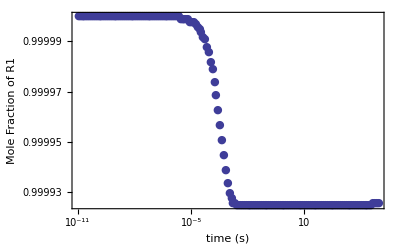

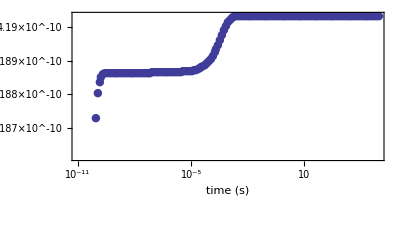

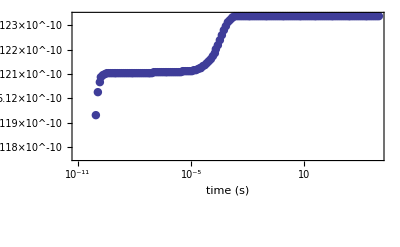

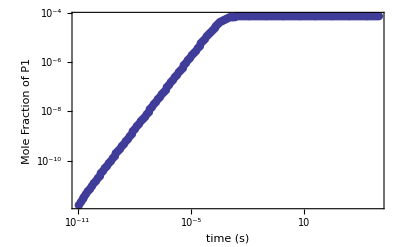

```mathematica
MESMERSpeciesProfilePlot[Profile]
```

```mathematica
rate=MESMERFitRate[Profile⟦1,2;;,{1,2}⟧,1]
```

{kf→0.200481,kb→2675.02}

```mathematica
rate⟦1,2⟧/(0.02* 1/1500/82.0574587 )
```

1.23382×10^6

```mathematica
AverEData=ReadMESMERAverageEnergy["P1_0T1500_0.test"];
```

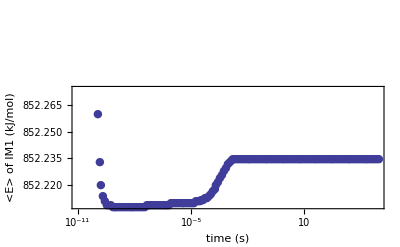

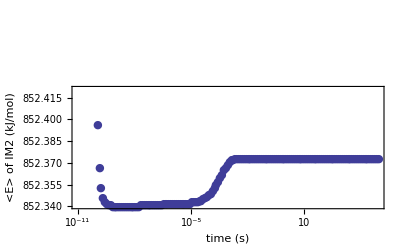

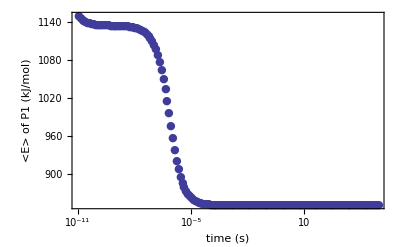

```mathematica
MESMERAverageEnergyPlot[AverEData]
```

```mathematica
ReadMESMEREquilFraction["P1_0T1500_0.test"]
```

{{IM1,4.19033×10^-10},{IM2,5.12341×10^-10},{P1,0.0000747742},{R1,0.999925}}

```mathematica
ReadMESMEREgienvalue["P1_0T1500_0.test"]
```

{-2.33587×10^7,-1.99141×10^7,-1.66743×10^7,-1.36163×10^7,-1.07317×10^7,-8.00511×10^6,-5.38598×10^6,-2.76469×10^6,-2670.06,7.2382×10^-12}

```mathematica
GrainedProfileData=ReadMESMERGrainedSpeciesProfile["P1_0T1500_0.test"]
```

```mathematica
MESMERGrainedSpeciesProfileManipulate[GrainedProfileData,"P1"]
```

## Global Setting

```mathematica
cwd = NotebookDirectory[];
SetDirectory[NotebookDirectory[]]
```

```mathematica
MESMERFileName=FileNames["*.test"]
```

```mathematica
Length[MESMERFileName]
```

## pT Grid one by one

For a fix p, the higher T,  the lower Kc, the lower P1(eq)/R1(eq), the larger rate const, the shorter time to equilibrium
For a fix T, the higher p, the higher P1(eq)/R1(eq), the larger rate const (for some temp which haven't yet its HPL), ... [ mole fraction C2H2 = 0.02]

### 0.1 atm, 1000K

#### Summary

0.1atm, 1000K
EgrainSize OK: deviated from cell's result by 1 in ten thousand.
TopEnergyHill OK: deviated from analytical result by 3 in one hundred.
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq) = 0.0015, is larger than 1 atm and 1500K.  Therefore, the Kc =  P1eq/R1eq/C2H2 = 0.00150121/0.998499/(0.02* 0.1/1000/82.0574587) = 61685.3 cc/mol. Kp ~ 1.
The largest eigenvalue is 0. The 2nd largest is -0.0344822, therefore, kf + kb should be 0.0344822. The fitting result shows this is indeed true.
The <E> of P1 reach its thermal equilibrium value between 0.1~1ms.
The reaction system reach its chemical equilibrium between 10 ~ 100 s. What a slow reaction !!!
Its bimolecular forward rate const: 2122.22 cc/mol/s. unimolecular backward rate const: 0.0344542 /s. rate const = HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦1⟧;
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1]
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 0.1/1000/82.0574587 )
```

```mathematica
MESMERGrainedSpeciesProfileManipulate[ReadMESMERGrainedSpeciesProfile [filename],"P1"]
```

```mathematica
MemoryInUse[]
```

### 0.1 atm, 1200K

#### Summary

0.1atm, 1200K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq) = 0.0001, 15 times smaller than 0.1 atm and 1000K.  Therefore, the Kc =  P1eq/R1eq/C2H2 =0.0001033180.999897/(0.02* 0.1/1200/82.0574587) = 5086.28 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is-9.43587, therefore, kf + kb should be 9.43587. The fitting result shows this is indeed true.
The <E> of P1 reach its thermal equilibrium value between 10^-5 ~ 10^-4 s.
The reaction system reach its chemical equilibrium between 0.01 ~ 0.1 s. What a slow reaction !!!
Its bimolecular forward rate const: 48087.9 cc/mol/s. unimolecular backward rate const: 9.47973 /s. rate const = HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦2⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1]
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 0.1/1200/82.0574587 )
```

```mathematica
MESMERGrainedSpeciesProfileManipulate[ReadMESMERGrainedSpeciesProfile [filename],"P1"]
```

```mathematica
MemoryInUse[]
```

### 0.1 atm, 1500K

#### Summary

0.1atm, 1500K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq) =7.47792×10^-6, decrease as temperature increase, since it is entropy decrease process.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =7.47792×10^-6/0.999993/(0.02* 0.1/1500/82.0574587) = 460.218 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -2361.32, therefore, kf + kb should be 2361.32. The fitting result shows this is indeed true.
The <E> of P1 reach its thermal equilibrium value between 10^-5 ~ 10^-4 s.
The reaction system reach its chemical equilibrium around 1 ms. 
Its bimolecular forward rate const: 1.14891×10^6 cc/mol/s. unimolecular backward rate const: 2644.49 /s. rate const = HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦3⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1]
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 0.1/1500/82.0574587 )
```

```mathematica
MESMERGrainedSpeciesProfileManipulate[ReadMESMERGrainedSpeciesProfile [filename],"P1"]
```

```mathematica
MemoryInUse[]
```

### 0.1 atm, 1800K

#### Summary

0.1atm, 1800K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq) =1.36001×10^-6, decrease as temperature increase, since it is entropy decrease process.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =1.36001×10^-6/0.999999/(0.02* 0.1/1800/82.0574587) = 100.439 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -41180.3, therefore, kf + kb should be ReadMESMERSpeicesProfile[filename]. The fitting result shows this is NO THE CASE !!!
The <E> of P1 reach its thermal equilibrium value between 10^-5 ~ 10^-4 s.
The reaction system reach its chemical equilibrium around 10^-5 ~ 10^-4 s. 
FitType = 1:
Its bimolecular forward rate const: 5.73536×10^6 cc/mol/s. unimolecular backward rate const: 77291.3 /s. Kc=5.73536×10^6/77291.3 cc/mol = 74.2045 cc/mol
2nd largest eigenvalue or rate fittings are wrong !!! Fitting by P1
Refit by FitType = 2: 
Its bimolecular forward rate const:5.02072×10^6cc/mol/s.unimolecular backward rate const:50064.7/s.Kc=5.02072×10^6/50064.7cc/mol=100.285 cc/mol. rate const != HPL
EigenValue problem:
The solution of the master equation should be a1*e^(-λ1*t)+a2*e^(-λ2*t)+a3*e^(-λ3*t)+a4*e^(-λ4*t)+...=a1 + a2*Exp[-41180.3*t]+ a3*Exp[-304941.*t]+ a4*Exp[-607490.*t]+...
Since the seperation of  λ3 and λ2 is not so large, therefore, the fitting kf+kb should be deviated from λ2 a little. In fact, from the master equation point of view, the pheomena rate const cannot be modelled by k_f/(k_f+k_b)(1-ⅇ^(-(k_f+k_b)t))

#### Analysis

```mathematica
filename=MESMERFileName⟦4⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1] (*FitType 1 -> incorrect*)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 0.1/1800/82.0574587 )
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2] (* FitType 2 -> better*)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 0.1/1800/82.0574587 )
```

```mathematica
MESMERGrainedSpeciesProfileManipulate[ReadMESMERGrainedSpeciesProfile [filename],"P1"]
```

```mathematica
MemoryInUse[]
```

### 0.1 atm, 2000K

#### Summary

0.1atm, 2000K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq)= 5.91926×10^-7, decrease as temperature increase, since it is entropy decrease process.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =5.91926×10^-7/0.999999/(0.02* 0.1/2000/82.0574587) =48.572 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -106497, 3rd largest is the same order of 2nd largest. Therefore, in principle, the rate const cannot be modelled as single exponential decay.
The <E> of P1 reach its thermal equilibrium value between 10^-5 ~ 10^-4 s.
The reaction system reach its chemical equilibrium around 10^-5 s. 
Refit by FitType = 2: 
Its bimolecular forward rate const:1.17913×10^7cc/mol/s.unimolecular backward rate const:244024./s.Kc=1.17913×10^7/244024.cc/mol=48.3203 cc/mol.   rate const != HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦5⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1] (*FitType 1 -> incorrect*)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 0.1/2000/82.0574587 )
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2] (* FitType 2 -> better*)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 0.1/2000/82.0574587 )
```

```mathematica
MESMERGrainedSpeciesProfileManipulate[ReadMESMERGrainedSpeciesProfile [filename],"P1"]
```

```mathematica
MemoryInUse[]
```

### 1.0 atm, 1000K

#### Summary

1.0atm, 1000K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq)=0.0148119/0.985188=0.0150346, decrease as temperature increase, increase as pressure increase.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =0.0148119/0.985188/(0.02* 1/1000/82.0574587) =61685. cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -0.0349482, kf+kb should be 0.0349482. Fitting result shows it is the case.
The <E> of P1 reach its thermal equilibrium value between 10^-5 s.
The reaction system reach its chemical equilibrium around 10 s. 
Its bimolecular forward rate const:2127.83cc/mol/s.unimolecular backward rate const:0.0344278/s.Kc=2127.83/0.0344278cc/mol=61805.6 cc/mol.   rate const = HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦11⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1] (*FitType 1 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 1.0/1000/82.0574587 )
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2] (* FitType 2 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 1.0/1000/82.0574587 )
```

```mathematica
MemoryInUse[]
```

### 1.0 atm, 1200K

#### Summary

1.0atm, 1200K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq)=0.00103222/0.998968=0.00103329, decrease as temperature increase, increase as pressure increase.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =0.00103222/0.998968/(0.02* 1/1200/82.0574587) =5087.33 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -9.46013, kf+kb should be 9.460132. Fitting result shows it is the case.
The <E> of P1 reach its thermal equilibrium value between 10^-5 s.
The reaction system reach its chemical equilibrium around 0.01 s. 
Its bimolecular forward rate const:48058.2cc/mol/s.unimolecular backward rate const:9.47851/s.Kc=48058.2/9.47851cc/mol=5070.23 cc/mol.   rate const = HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦12⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1] (*FitType 1 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 1.0/1200/82.0574587 )
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2] (* FitType 2 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 1.0/1200/82.0574587 )
```

```mathematica
MemoryInUse[]
```

### 1.0 atm, 1500K

#### Summary

1.0atm, 1500K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq)=0.0000747742/0.999925=0.0000747798, decrease as temperature increase, increase as pressure increase.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =0.0000747742/0.999925/(0.02* 1/1500/82.0574587) =460.218 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -2670.06, kf+kb should be 2670.06. Fitting result shows it is the case.
The <E> of P1 reach its thermal equilibrium value between 10^-5 s.
The reaction system reach its chemical equilibrium around 10^-4~ 10^-3 s. 
Its bimolecular forward rate const:1.22839×10^6cc/mol/s.unimolecular backward rate const:2675.02/s.Kc=1.22839×10^6/2675.02cc/mol=459.206 cc/mol.   rate const = HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦13⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1] (*FitType 1 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 1.0/1500/82.0574587 )
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2] (* FitType 2 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 1.0/1500/82.0574587 )
```

```mathematica
MemoryInUse[]
```

### 1.0 atm, 1800K

#### Summary

1.0atm, 1800K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq)=0.0000136/0.999986=0.0000136002, decrease as temperature increase, increase as pressure increase.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =0.0000136/0.999986/(0.02* 1/1800/82.0574587) =100.44 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -87315.8,  3rd largest is the same order of 2nd largest. Therefore, in principle, the rate const cannot be modelled as single exponential decay.
The <E> of P1 reach its thermal equilibrium value between 10^-5 s.
The reaction system reach its chemical equilibrium around 10^-5 s, which is the same order of thermal equilibrium. It causes 2nd and 3rd largest eigenvalues are the same order.
Its bimolecular forward rate const:8.58104×10^6cc/mol/s.unimolecular backward rate const:82953./s.Kc=8.58104×10^6/82953.cc/mol=103.444 cc/mol.   rate const != HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦14⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1] (*FitType 1 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 1.0/1800/82.0574587 )
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2] (* FitType 2 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 1.0/1800/82.0574587 )
```

```mathematica
MemoryInUse[]
```

### 1.0 atm, 2000K

#### Summary

1.0atm, 2000K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq)=5.91923×10^-6/0.999994=5.91927×10^-6, decrease as temperature increase, increase as pressure increase.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =5.91923×10^-6/0.999994/(0.02* 1/2000/82.0574587) =48.572 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -334174.,   3rd largest is the same order of 2nd largest. Therefore, in principle, the rate const cannot be modelled as single exponential decay.
The <E> of P1 reach its thermal equilibrium value between 10^-5 s.
The reaction system reach its chemical equilibrium around 10^-5 s, which is the same order of thermal equilibrium. It causes 2nd and 3rd largest eigenvalues are the same order.
Its bimolecular forward rate const:1.98474×10^7cc/mol/s.unimolecular backward rate const:404487./s.Kc=1.98474×10^7/404487.cc/mol=49.0681 cc/mol.   rate const != HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦15⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1] (*FitType 1 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 1.0/2000/82.0574587 )
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2] (* FitType 2 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 1.0/2000/82.0574587 )
```

```mathematica
MESMERGrainedSpeciesProfileManipulate[ReadMESMERGrainedSpeciesProfile [filename],"IM1"]
```

```mathematica
MemoryInUse[]
```

### 10.0 atm, 1000K

#### Summary

10.0atm, 1000K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq)=0.130697/0.869303=0.150347, decrease as temperature increase, increase as pressure increase.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =0.130697/0.86930/(0.02* 10/1000/82.0574587) =61685.6 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -0.0395994,  kf+kb should be 0.0395994. Fitting result shows it is the case.
The <E> of P1 reach its thermal equilibrium value between 10^-6 s.
The reaction system reach its chemical equilibrium around 10 s.
Its bimolecular forward rate const:2108.9cc/mol/s.unimolecular backward rate const:0.033942/s.Kc=2108.9/0.033942cc/mol=62132.7 cc/mol.   rate const = HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦6⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1] (*FitType 1 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 10/1000/82.0574587 )
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2] (* FitType 2 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 10/1000/82.0574587 )
```

```mathematica
MemoryInUse[]
```

### 10.0 atm, 1200K

#### Summary

10.0atm, 1200K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq)=0.0102272/0.989773=0.0103329, decrease as temperature increase, increase as pressure increase.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =0.0102272/0.989773/(0.02* 10/1200/82.0574587) 5087.34 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -9.54953,  kf+kb should be 9.54953. Fitting result shows it is the case.
The <E> of P1 reach its thermal equilibrium value between 10^-6 s.
The reaction system reach its chemical equilibrium around 0.1 s.
Its bimolecular forward rate const:48599.7cc/mol/s.unimolecular backward rate const:9.67263/s.Kc=48599.7/9.67263cc/mol=5024.46 cc/mol.   rate const = HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦7⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1] (*FitType 1 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 10/1200/82.0574587 )
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2] (* FitType 2 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 10/1200/82.0574587 )
```

```mathematica
MemoryInUse[]
```

### 10.0 atm, 1500K

#### Summary

10.0atm, 1500K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq)=0.000747239/0.999253=0.000746681, decrease as temperature increase, increase as pressure increase.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =0.000747239/0.999253/(0.02* 10/1500/82.0574587)=460.218 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -2719.98,  kf+kb should be 2719.98. Fitting result shows it is the case.
The <E> of P1 reach its thermal equilibrium value between 10^-5 s.
The reaction system reach its chemical equilibrium around 0.1 ~ 1 ms.
Its bimolecular forward rate const:1.26442×10^6cc/mol/s.unimolecular backward rate const:2717.91/s.Kc=1.26442×10^6/2717.91cc/mol=465.217 cc/mol.   rate const = HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦8⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1] (*FitType 1 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 10/1500/82.0574587 )
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2] (* FitType 2 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 10/1500/82.0574587 )
```

```mathematica
MemoryInUse[]
```

### 10.0 atm, 1800K

#### Summary

10.0atm, 1800K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq)=0.000135983/0.999864=0.000136001, decrease as temperature increase, increase as pressure increase.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =0.000135983/0.999864/(0.02* 10/1800/82.0574587)=100.439 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -115386.,  kf+kb should be115386. Fitting result shows it is the case.
The <E> of P1 reach its thermal equilibrium value between 10^-5 s.
The reaction system reach its chemical equilibrium around 0.01 ms.
Its bimolecular forward rate const:1.15844×10^7cc/mol/s.unimolecular backward rate const:115351./s.Kc=1.15844×10^7/115351.cc/mol=100.427 cc/mol.   rate const = HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦9⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1] (*FitType 1 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 10/1800/82.0574587 )
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2] (* FitType 2 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 10/1800/82.0574587 )
```

```mathematica
MemoryInUse[]
```

### 10.0 atm, 2000K

#### Summary

10.0atm, 2000K
EgrainSize OK
TopEnergyHill OK
QSS approximation holds well for IM1 and IM2
P1(eq)/R1(eq)=0.0000591892/0.999941=0.0000591927, decrease as temperature increase, increase as pressure increase.  
Therefore, the Kc =  P1eq/R1eq/C2H2 =0.0000591892/0.999941/(0.02* 10/2000/82.0574587)=48.572 cc/mol. Agree with the result of Thermo Keq
The largest eigenvalue is 0. The 2nd largest is -646176,  kf+kb should be 646176. Fitting result shows it is the case.
The <E> of P1 reach its thermal equilibrium value between 10^-5 s.
The reaction system reach its chemical equilibrium around 10^-6 s.
Its bimolecular forward rate const:3.18928×10^7cc/mol/s.unimolecular backward rate const:656810./s.Kc=3.18928×10^7/656810.cc/mol=48.5571 cc/mol.   rate const != HPL

#### Analysis

```mathematica
filename=MESMERFileName⟦10⟧
```

```mathematica
ReadMESMERpT[filename]
ReadMESMERGrainTopHillTest[filename]
ReadMESMEREquilFraction [filename]
ReadMESMEREgienvalue [filename]
```

```mathematica
ReadMESMERAverageEnergy [filename]//MESMERAverageEnergyPlot
```

```mathematica
profile=ReadMESMERSpeicesProfile[filename];
MESMERSpeciesProfilePlot[profile]
```

```mathematica
profile⟦1,1⟧
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,2}⟧,1] (*FitType 1 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 10/2000/82.0574587 )
```

```mathematica
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2] (* FitType 2 *)
```

```mathematica
bioratefor=rate⟦1,2⟧/(0.02* 10/2000/82.0574587 )
```

```mathematica
MemoryInUse[]
```

## pT Fitting

```mathematica
pTrate=Table[{0,0,0,0},{i,1,Length[MESMERFileName]}]; (*{ p, T, kf, kb }*)
For[i=1,i≤ Length[MESMERFileName],i++,
filename=MESMERFileName⟦i⟧;
pTpair=ReadMESMERpT[filename]⟦{2,3}⟧;
pTrate⟦i,{1,2}⟧=pTpair;
profile=ReadMESMERSpeicesProfile[filename];
rate=MESMERFitRate[profile⟦1,2;;,{1,5}⟧,2];
rate⟦1,2⟧=rate⟦1,2⟧/(0.02* pTpair⟦1⟧/pTpair⟦2⟧/82.0574587 );
pTrate⟦i,3⟧=rate⟦1,2⟧;
pTrate⟦i,4⟧=rate⟦2,2⟧;
]
```

```mathematica
pTrate//TraditionalForm
```

```mathematica
(*tell how many pressure*)
pList={};
For[i=1,i≤ Length[pTrate],i++,
If[MemberQ[pList,Round[pTrate⟦i,1⟧*100]/100.0]==False,
AppendTo[pList,Round[pTrate⟦i,1⟧*100]/100.0]
]
];
pList
```

```mathematica
(* 2-parameter-fitting at first*)
Trate=Table[{},{i,1,Length[pList]}]; (* Trate⟦i⟧ stores k(T) at pi *)
pTFitkfor2p=Table[{},{i,1,Length[pList]}]; 
pTFitkbac2p=Table[{},{i,1,Length[pList]}]; 
For[i=1,i≤ Length[pList],i++,
For[j=1,j≤ Length[pTrate],j++,
If [Abs[pTrate⟦j,1⟧/pList⟦i⟧-1]<0.01,AppendTo[Trate⟦i⟧,pTrate⟦j,2;;4⟧]]
];
(*pTFitkfor⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,2}⟧,A*β^n*ⅇ^(-Ea*β),{A,n,Ea},β,MaxIterations-> 100000]];
pTFitkbac⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,3}⟧,A*β^n*ⅇ^(-Ea*β),{A,n,Ea},β,MaxIterations-> 100000]]*)
(*fortemp=NonlinearModelFit[Trate⟦i,All,{1,2}⟧,A*ⅇ^(-Ea/T),{A,n,Ea},T,MaxIterations-> 100000];
pTFitkfor2p⟦i⟧=fortemp["BestFitParameters"];
bactemp=NonlinearModelFit[Trate⟦i,All,{1,3}⟧,A*ⅇ^(-Ea/T),{A,n,Ea},T,MaxIterations-> 100000];
pTFitkbac2p⟦i⟧=bactemp["BestFitParameters"]*)
pTFitkfor2p⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,2}⟧,A*ⅇ^(-Ea/T),{A,n,Ea},T,MaxIterations-> 100000]];
pTFitkbac2p⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,3}⟧,A*ⅇ^(-Ea/T),{A,n,Ea},T,MaxIterations-> 100000]]
];
Trate
pTFitkfor2p
pTFitkbac2p
```

```mathematica
(*3-parameter-fitting*)
Trate=Table[{},{i,1,Length[pList]}]; (* Trate⟦i⟧ stores k(T) at pi *)
pTFitkfor=Table[{},{i,1,Length[pList]}]; 
pTFitkbac=Table[{},{i,1,Length[pList]}]; 
For[i=1,i≤ Length[pList],i++,
For[j=1,j≤ Length[pTrate],j++,
If [Abs[pTrate⟦j,1⟧/pList⟦i⟧-1]<0.01,AppendTo[Trate⟦i⟧,pTrate⟦j,2;;4⟧]]
];
(*pTFitkfor⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,2}⟧,A*β^n*ⅇ^(-Ea*β),{A,n,Ea},β,MaxIterations-> 100000]];
pTFitkbac⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,3}⟧,A*β^n*ⅇ^(-Ea*β),{A,n,Ea},β,MaxIterations-> 100000]]*)
(*pTFitkfor⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,2}⟧,A*T^n*ⅇ^(-Ea/T),{{A,pTFitkfor2p⟦i,1,2⟧},n,{Ea,pTFitkfor2p⟦i,3,2⟧}},T,MaxIterations-> 100000]];
pTFitkbac⟦i⟧=Normal[NonlinearModelFit[Trate⟦i,All,{1,3}⟧,A*T^n*ⅇ^(-Ea/T),{{A,pTFitkbac2p⟦i,1,2⟧},n,{Ea,pTFitkbac2p⟦i,3,2⟧}},T,MaxIterations-> 100000]]*)
pTFitkfor⟦i⟧=Simplify[Exp[Normal[NonlinearModelFit[{#⟦1⟧,Log[#⟦2⟧]}&/@Trate⟦i,All,{1,2}⟧,A+n*Log[T]-Ea/T,{A,n,Ea},T,MaxIterations-> 100000]]]];
pTFitkbac⟦i⟧=Normal[NonlinearModelFit[{#⟦1⟧,Log[#⟦2⟧]}&/@Trate⟦i,All,{1,3}⟧,A+n*Log[T]-Ea/T,{A,n,Ea},T,MaxIterations-> 100000]]//Exp//Simplify;
];
Trate
pTFitkfor
pTFitkbac
```

```mathematica
(*forward kf(T) at pi, plot*)
For[i=1,i≤ Length[pList],i++,
plotframeKeqT={{Style["kf (cc/mol/s) ",Italic,17],},{Style["Temperature (K), p ="<>ToString[pList⟦i⟧]<>"atm",Italic,17],}};
plot1=ListLogPlot[Trate⟦i,All,{1,2}⟧,
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframeKeqT,FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,
                  PlotMarkers-> {Automatic,Medium}];
plot2=LogPlot[pTFitkfor⟦i⟧,{T,1000,2000},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframeKeqT,FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed];
Show[plot1,plot2]//Print
]
```

```mathematica
(*backward kb(T) at pi, plot*)
For[i=1,i≤ Length[pList],i++,
plotframeKeqT={{Style["kb (1/s) ",Italic,17],},{Style["Temperature (K), p ="<>ToString[pList⟦i⟧]<>"atm",Italic,17],}};
plot1=ListLogPlot[Trate⟦i,All,{1,3}⟧,
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframeKeqT,FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed,
                  PlotMarkers-> {Automatic,Medium}];
plot2=LogPlot[pTFitkbac⟦i⟧,{T,1000,2000},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframeKeqT,FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed];
Show[plot1,plot2]//Print
]
```

```mathematica
CTSTsub={k1f->12448.554994205466 ⅇ^(-10123.73598478263/T) T^2.5756906282734318 ,k2f-> 1.2314159585309521*^13 ⅇ^(-1619.7882016887015/T) T^0.07882932923431851,k3f->4.928724024018525*^10 ⅇ^(-13359.388983637935/T) T^0.5615720564813181 ,k1b->6.932850830900494*^13 ⅇ^(-7694.442320234193/T) T^0.09763011847559883 ,k2b->1.3356622920909986*^13 ⅇ^(-1871.0111791780876/T) T^0.06605332874706629,k3b->2.651265579830942*^11 ⅇ^(-33397.523778289215/T) T^0.52823064019746  };
```

```mathematica
HPLkfor=(k1f k2f k3f)/(k1b k2b)/.CTSTsub
```

```mathematica
HPLkbac=k3b/.CTSTsub
```

```mathematica
pIverseTFitkfor=AppendTo[pTFitkfor,HPLkfor]/.(T-> 1000/β);
plotframeKeqT={{Style["k_f (cc/mol/s) ",Italic,17],},{Style["1000 K/Temperature",Italic,17],}};
pIverseTFitkforPlot=LogPlot[pIverseTFitkfor,{β,0.5,1},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframeKeqT,FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed]
(*Blue 0.1 atm. Yellow 1.0 atm. Purple 10.0 atm. Green HPL*)
```

```mathematica
pIverseTFitkbac=AppendTo[pTFitkbac,HPLkbac]/.(T-> 1000/β);
plotframeKeqT={{Style["k_b (1/s) ",Italic,17],},{Style["1000 K/Temperature",Italic,17],}};
pIverseTFitkbacPlot=LogPlot[pIverseTFitkbac,{β,0.5,1},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframeKeqT,FrameTicksStyle->16,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->Dashed]
(*Blue 0.1 atm. Yellow 1.0 atm. Purple 10.0 atm. Green HPL*)
```

## Summary

```mathematica
AppendTo[pList,∞];
```

```mathematica
AppendTo[pTFitkfor,HPLkfor];
```

```mathematica
AppendTo[pTFitkbac,HPLkbac];
```

```mathematica
summary=Table[0,{j,1,3},{i,1,Length[pList]+1}];
summary⟦1⟧={"p"}; For[i=1,i≤ Length[pList],i++,AppendTo[summary⟦1⟧,pList⟦i⟧]];
summary⟦2⟧={"k_f(cc/mol/s)"};For[i=1,i≤ Length[pList],i++,AppendTo[summary⟦2⟧,pTFitkfor⟦i⟧]];
summary⟦3⟧={"k_b(1/s)"};For[i=1,i≤ Length[pList],i++,AppendTo[summary⟦3⟧,pTFitkbac⟦i⟧]];
summary//TraditionalForm
```

```mathematica
pIverseTFitkforPlot
```

```mathematica
pIverseTFitkbacPlot
```